```mathematica
Clear["Global`*"]
```

```mathematica
f[t_,A_,T_]:=Module[
{tt},
tt:=Mod[t,T];
Piecewise[{{-A/2+(2A)/T tt, tt<T/2}, {A/2-(tt-T/2)(2A)/T, tt≥T/2}}]
]
```

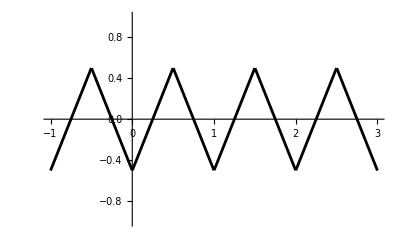

```mathematica
Plot[f[t,1,1],{t,-1,3}, 
PlotRange ->{-1,1},
PlotStyle -> {Black,Thickness[0.005]}
]
```

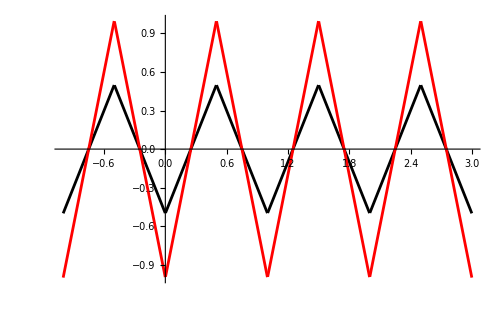

```mathematica
Plot[{f[t,1,1],f[t,2,1]},{t,-1,3}, 
PlotRange ->{-1,1},
PlotStyle -> {{Black,Thickness[0.004]},
{Red, Thickness[0.004]}},
ImageSize->500
]
```

```mathematica
f1[t_]:=f[t,1,1];
f2[t_]:=f[t,2,1];
c[t_]:=Sign[f1[t]-f2[t]];
```

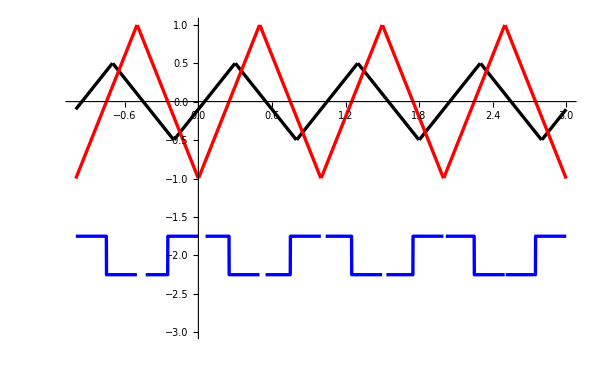

```mathematica
Plot[{f1[t+0.2],f2[t],-2+c[t]/4},{t,-1,3}, 
PlotRange ->{-3,1},
PlotStyle -> {
{Black,Thickness[0.004]},
{Red, Thickness[0.004]},
{Blue, Thickness[0.004]}
},
ImageSize->600
]
```

```mathematica
Manipulate[
Plot[{f1[t+ϕ],f2[t],-2+c[t]/4},{t,-1,3}, 
PlotRange ->{-3,1},
PlotStyle -> {
{Black,Thickness[0.004]},
{Red, Thickness[0.004]},
{Blue, Thickness[0.004]}
},
ImageSize->600
],
{{ϕ,1/2},0,1},
{{d,1/2},0,1}
]
```

```mathematica
Solve[
f1[t]==f2[t],
t
]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[Piecewise[{{-1/2+2 Mod[t,1], Mod[t,1]<1/2}, {1/2-2 (-1/2+Mod[t,1]), Mod[t,1]≥1/2}, {0, True}}]==Piecewise[{{-1+4 Mod[t,1], Mod[t,1]<1/2}, {1-4 (-1/2+Mod[t,1]), Mod[t,1]≥1/2}, {0, True}}],t]